(stelar) objects :
OverVector[r_i](t)=(r⃗)_(0i)+ρ_i (cos(ω_i t)
sin(ω_i t))

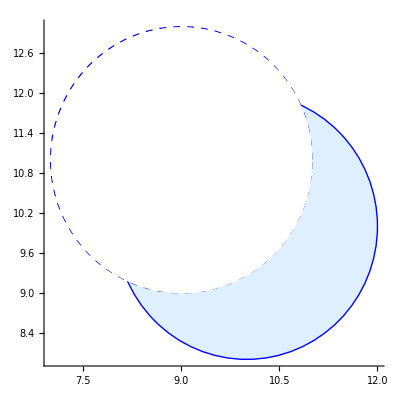

```mathematica
Subscript[ρ, 1]=2;
Subscript[r, 01]={10,10};
Subscript[ω, 1]=2;
Subscript[ρ, 2]=2;
Subscript[r, 02]={9,11};
Subscript[ω, 2]=2;
Graphics[{LightBlue,Disk[Subscript[r, 01],Subscript[ρ, 1]],Blue,Circle[Subscript[r, 01],Subscript[ρ, 1]],Dashed,Thick,Circle[Subscript[r, 02],Subscript[ρ, 2]],White,Disk[Subscript[r, 02],Subscript[ρ, 2]]},Axes->True]
```

```mathematica
(*Define the cone with axis along x-axis*)cones=ParametricPlot3D[{{2 u,u Cos[0.5 v],u Sin[0.5 v]},{u,u Cos[v],u Sin[v]}},{u,0,1},{v,0,2 Pi},PlotStyle->{Directive[Orange,Specularity[White,10]],Green},MeshFunctions->{#1&,#2&}];

(*Define the rotation around the z-axis*)
rotation=Table[Graphics3D[GeometricTransformation[cones[[1]],RotationTransform[θ,{0,0,1}]]],{θ,0,2 Pi,Pi/20}];

(*Animate the rotating cone*)
ListAnimate[rotation,AnimationRunning->False]
```

```mathematica
pathA[var_]:=CoordinateTransformData["Spherical"->"Cartesian","Mapping",{1,Exp[-15 (var-π/2)^4]+Pi/4,0.5 ArcTan[20 (var-π/2)]+π/4}]
pathB[var_]:=CoordinateTransformData["Spherical"->"Cartesian","Mapping",{var,Exp[-5 (var-π/2)^4]+Pi/4,0.15 ArcTan[20 (var-π/2)]+π/4}]


With[{g=ParametricPlot3D[{pathA@u,pathB@u},{u,1/4 π,3/4 Pi},PlotStyle->{Gray,Dashed}]},Animate[Show[g,Graphics3D[{Arrow[{{0,0,0},pathA[v]}],Red,PointSize[0.05],Point[pathA@v]}],Graphics3D[{Arrow[{{0,0,0},pathB[v]}],Blue,PointSize[0.05],Point[pathB@v]}]],{v,1/4 π,3/4 Pi,π/50},AnimationRunning->False]]
```

```mathematica
rt[t_,ϵ_,P_,a_,ϕ_:0]:=
Module[{},
n=2 π/P;
eE=ee/.NSolve[n t==ee-ϵ Sin[ee],ee,Reals][[1]];
th=2 ArcTan[Tan[eE/2] √((1+ϵ)/(1-ϵ))];
(*th=θ/.NSolve[(1-ϵ) Tan[θ/2]^2==(1+ϵ) Tan[eE/2]^2,θ,Reals][[1]];*)
(*th=Mod[th,π];
If[Abs[th]<10^-5,th=10^-3];*)
If[th<0,th=th];
{a (1-ϵ Cos[eE]),ϕ,th}
]
rt[1,0.0,3,10.1,1]
```

{10.1,1,2.0944}

```mathematica
CoordinateTransformData["Spherical"->"Cartesian","Mapping",{3.1994846800370365,1,-1}]
```

{1.45464,-2.26547,1.72869}

```mathematica
coords=Table[CoordinateTransformData["Spherical"->"Cartesian","Mapping",rt[tt,0.6,100.5,2,1]],{tt,0,100}];
ListPlot3D[coords,Mesh->All]
```

-Graphics3D-

```mathematica
ϵ1=0.1; (* circular *)
ϵ2=0.1; (* eliptical *)
Period1=3;
Period2=3; (* faster *)
a1=2;
a2=2.1; (* semi-major axes *)
tilt1=0.1; tilt2=0.15;
R1=0.05; (* planetary radius *)
R2=0.9 R1;
pathC1[var_]:=CoordinateTransformData["Spherical"->"Cartesian","Mapping",rt[var,ϵ1,Period1,a1,tilt1]]
pathC2[var_]:=CoordinateTransformData["Spherical"->"Cartesian","Mapping",rt[var,ϵ2,Period2,a2,tilt2]]

With[{g=ParametricPlot3D[{pathC1@u,pathC2@u},{u,0,Max[{Period1,Period2}]},PlotStyle->{{Gray,Dashed},{Black,Dashed}},PlotRange->All]},Animate[Show[g,Graphics3D[{Arrowheads[0.01],Arrow[{{0,0,0},pathC1[v]}],Red,PointSize[R1],Point[pathC1@v]},BoxRatios->1],Graphics3D[{Arrowheads[0.01],Arrow[{{0,0,0},pathC2[v]}],Yellow,PointSize[R2],Point[pathC2@v]},BoxRatios->1]],{v,0,Max[{Period1,Period2}],π/50},AnimationRunning->False]]
```